```mathematica
(*Tomando que xf = ln(0.038  mpl m g/(√gast)) y λ = 0.263  mpl m gasts/(√gast), podemos obtener una expresión para Yinf = xf/λ:
m Yinf = m (ln(0.038  mpl m g/(√gast)))/(0.263  mpl m gasts/(√gast)), donde hemos multiplicado por 'm' a ambos lados de la igualdad.
Definiendo la constante k = 0.038 mpl g/(√gast), reescribimos nuestra expresión para m Yinf:
m Yinf = (ln(k m ))/(0.263  mpl gasts/(√gast)),
=>  m Yinf = (3.802 √gast)/(mpl gasts)ln(k m ),
=> (3.802 √gast)/(mpl gasts)ln(k m ) -  m Yinf = 0.

De esta última expresión despejamos  en función de m, en donde si consideramos que la abundancia de materia oscura final 'm Yinf' es fija, obtendremos una relación únicamente entre estas dos variables.
*)
```

```mathematica
gast=100;
gasts=100;
g=1;

ec=1.602177*10^-19;
c=299792458 ; 

mpl=2.17651*10^-8; (*Kg*)
mpl=(mpl c^2)/(ec *10^9) ;(*GeV*)


k=(0.038*mpl g)/(√gast);
mYinf=10^0;

(*Definimos nuestras constantes*)
```

```mathematica
sol=Solve[(3.802 √gast)/(mpl gasts)(Log[k σ m])-σ mYinf==0,σ] (*Despejamos  de la ecuación*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{σ→-3.11401×10^-20 ProductLog[-692.156/m]}}

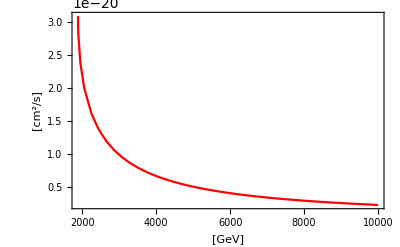

```mathematica
Plot[σ/. sol[[1]],{m,10,10^4},PlotRange->{Automatic,Full},PlotStyle->{Red},PlotTheme->"Scientific",FrameLabel->{Style[" [GeV]",Black,13],Style["[cm^2/s]",Black,13]},FrameStyle->Black]
```